# Muon Production in SM - γ-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
Quit[]
```

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SMbgf",GenericModel->"Lorentzbgf",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{4,5}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

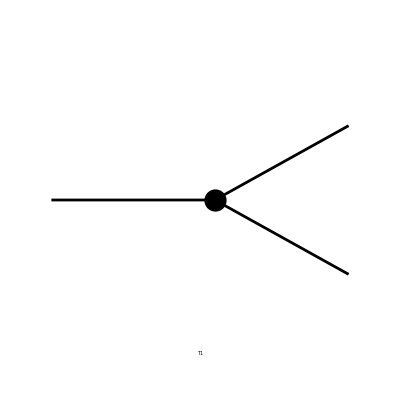

```mathematica
tops=CreateTopologies[0,1->2,Adjacencies->3];
Paint[tops];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

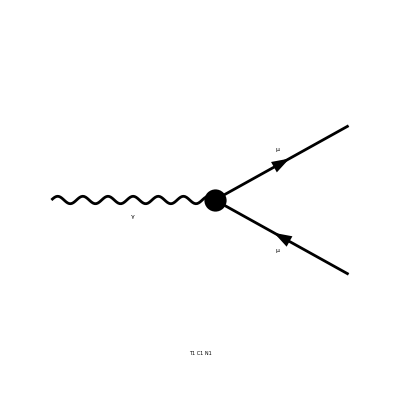

```mathematica
ins=InsertFields[tops, process];
Paint[ins];
```

## Feynman Amplitudes

```mathematica
amp=CreateFeynAmp[ins,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

## FormCalc results

```mathematica
ClearProcess[]
```

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL (F1+F2)]

```mathematica
UVDivergentPart[result]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

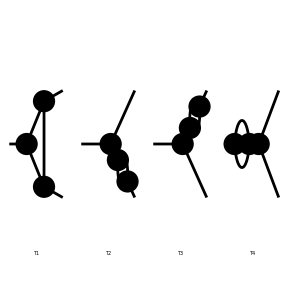

```mathematica
tops1=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

## Insertions

Excluding 2 Generic, 31 Classes, and 35 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 4: 1 Generic, 6 Classes, 18 Particles insertions

Restoring 2 Generic, 31 Classes, and 35 Particles fields

in total: 4 Generic, 9 Classes, 21 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

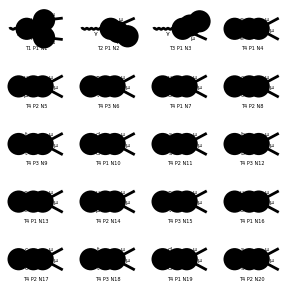

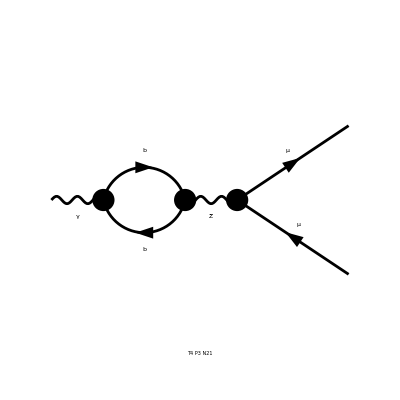

```mathematica
ins1=InsertFields[tops1, process,QEDOnly];
Paint[ins1, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 18 Particles amplitudes

in total: 21 Particles amplitudes

## FormCalc results

```mathematica
result1=CalcFeynAmp[amp1]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/π Alfa EL (-Sub5 (C0i[cc1,MM2,0,MM2,0,MM2,MM2]+C0i[cc2,MM2,0,MM2,0,MM2,MM2])+(F3+F4) MM Pair1 (C0i[cc11,MM2,0,MM2,0,MM2,MM2]+2 C0i[cc12,MM2,0,MM2,0,MM2,MM2]+C0i[cc22,MM2,0,MM2,0,MM2,MM2])+(F1+F2) (Finite/4-1/2 B0i[bb0,MM2,0,MM2]+C0i[cc00,MM2,0,MM2,0,MM2,MM2]+(A0[ME2]+A0[ML2]+A0[MM2]+1/3 (A0[MB2]+A0[MD2]+A0[MS2])+4/3 (A0[MC2]+A0[MT2]+A0[MU2])-2 (B0i[bb00,0,ME2,ME2]+B0i[bb00,0,ML2,ML2]+B0i[bb00,0,MM2,MM2])-2/3 (B0i[bb00,0,MB2,MB2]+B0i[bb00,0,MD2,MD2]+B0i[bb00,0,MS2,MS2])-8/3 (B0i[bb00,0,MC2,MC2]+B0i[bb00,0,MT2,MT2]+B0i[bb00,0,MU2,MU2])) Den[0,0]+MM2 (-C0i[cc0,MM2,0,MM2,0,MM2,MM2]+(Finite-2 B0i[bb0,MM2,0,MM2]+2 B0i[bb1,MM2,0,MM2]) Den[MM2,MM2]))+1/CW2(Sub4 (1/8 (A0[ME2]+A0[ML2]+A0[MM2])+1/4 (-B0i[bb00,0,ME2,ME2]-B0i[bb00,0,ML2,ML2]-B0i[bb00,0,MM2,MM2]))+Sub2 (1/24 (A0[MB2]+A0[MD2]+A0[MS2])+1/12 (-B0i[bb00,0,MB2,MB2]-B0i[bb00,0,MD2,MD2]-B0i[bb00,0,MS2,MS2]))+Sub3 (1/12 (A0[MC2]+A0[MT2]+A0[MU2])+1/6 (-B0i[bb00,0,MC2,MC2]-B0i[bb00,0,MT2,MT2]-B0i[bb00,0,MU2,MU2]))) Den[MZ2,0])]

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
selectFeynAmp[amp_,i_Integer/;i≥0]:=amp[[0]][amp[[i]]]
```

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#]]&,amp]
```

## Computations

```mathematica
Length[amp1]
```

12

```mathematica
result1List=calcFeynAmpList[amp1]/.result1List[[0]]->List;
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDiv=Map[UVDivergentPart,result1List]
```

```mathematica
uvDiv=Map[#[[1]]&,uvDiv]
```

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SMbgf},GenericModel→{Lorentzbgf},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],S[10],S[20],-S[30],S[30],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Mix[S,V][20],-Mix[S,V][30],Mix[S,V][30],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3],Rev[S,V][20],-Rev[S,V][30],Rev[S,V][30]},ExcludeFieldPoints→{},LastSelections→{}][-(Alfa Divergence EL (F1+F2))/(4 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0]

```mathematica
Abbr[]
```

{F3→(u̇ 2|6|v3),F4→(u̇ 2|7|v3),F1→(u̇ 2|6,e[1]|v3),F2→(u̇ 2|7,e[1]|v3),Pair1→Pair[e[1],k[2]]}

```mathematica
??EL
```

## CounterTerms

## CT Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

> Top. 2 ad/bdce/ed.m, 0 diagrams

> Top. 3 ad/becd/ed.m, 0 diagrams

> Top. 4 ad/bece/de.m, 0 diagrams

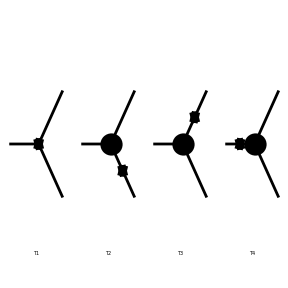

```mathematica
cttops=CreateCTTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->TadpoleCTs];
Paint[cttops];
```

## Insertions

Excluding 2 Generic, 31 Classes, and 35 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 0 Generic, 0 Classes, 0 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 4: 0 Generic, 0 Classes, 0 Particles insertions

Restoring 2 Generic, 31 Classes, and 35 Particles fields

in total: 2 Generic, 2 Classes, 2 Particles insertions

> Top. 1 ad/bdce/ed.m, 0 diagrams

> Top. 2 ad/becd/ed.m, 0 diagrams

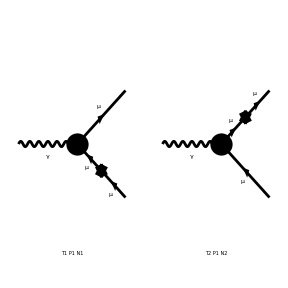

```mathematica
ctins=InsertFields[cttops, process,QEDOnly];
Paint[ctins, PaintLevel->{Particles}];
```

## Feynman Amplitudes

```mathematica
ctamp=CreateFeynAmp[ctins,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SMbgf},GenericModel→{Lorentzbgf},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],S[10],S[20],-S[30],S[30],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Mix[S,V][20],-Mix[S,V][30],Mix[S,V][30],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3],Rev[S,V][20],-Rev[S,V][30],Rev[S,V][30]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],-ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[-(k2)]).(-1/2 ⅈ (MM dZfR1[2,2,2]^*+2 dMf1[2,2]+MM dZfL1[2,2,2]) om_--1/2 ⅈ (MM dZfL1[2,2,2]^*+2 dMf1[2,2]+MM dZfR1[2,2,2]) om_++1/2 ⅈ (dZfR1[2,2,2]^*+dZfR1[2,2,2]) gs[-(k2)].om_+-1/2 ⅈ (dZfL1[2,2,2]^*+dZfL1[2,2,2]) gs[k2].om_-).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k2)^2)],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==2],Integral[],-ū[k1,MM].(-1/2 ⅈ (MM dZfR1[2,2,2]^*+2 dMf1[2,2]+MM dZfL1[2,2,2]) om_--1/2 ⅈ (MM dZfL1[2,2,2]^*+2 dMf1[2,2]+MM dZfR1[2,2,2]) om_+-1/2 ⅈ (dZfL1[2,2,2]^*+dZfL1[2,2,2]) gs[-(k1)].om_-+1/2 ⅈ (dZfR1[2,2,2]^*+dZfR1[2,2,2]) gs[k1].om_+).(MM+gs[k1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k1)^2)]]

> Top. 4: 1 Particles amplitude

in total: 4 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ ū[k1,MM].(ⅈ EL (dZAA1/2+dZe1+(dZZA1 (-1/2+SW2))/(2 CW SW)+1/2 dZfL1[2,2,2]^*+1/2 dZfL1[2,2,2]) ga[Lor1].om_-+ⅈ EL (dZAA1/2+dZe1+(dZZA1 SW)/(2 CW)+1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1]],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==2],Integral[],-ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[-(k2)]).(ⅈ (-1/2 MM dZfR1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfL1[2,2,2]) om_-+ⅈ (-1/2 MM dZfL1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfR1[2,2,2]) om_++ⅈ (1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) gs[-(k2)].om_++ⅈ (-1/2 dZfL1[2,2,2]^*-1/2 dZfL1[2,2,2]) gs[k2].om_-).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k2)^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==3],Integral[],-ū[k1,MM].(ⅈ (-1/2 MM dZfR1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfL1[2,2,2]) om_-+ⅈ (-1/2 MM dZfL1[2,2,2]^*-dMf1[2,2]-1/2 MM dZfR1[2,2,2]) om_++ⅈ (-1/2 dZfL1[2,2,2]^*-1/2 dZfL1[2,2,2]) gs[-(k1)].om_-+ⅈ (1/2 dZfR1[2,2,2]^*+1/2 dZfR1[2,2,2]) gs[k1].om_+).(MM+gs[k1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1] 1/(-MM2+(k1)^2)],FeynAmp[GraphID[Topology==4,Generic==1,Particles==1,Number==4],Integral[],ū[k1,MM].(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).v[k2,MM] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(k1+k2)^2 (-ⅈ dZAA1 (p1)[Lor2] (-(k1)-k2)[Lor1]+ⅈ dZAA1 g[Lor1,Lor2] (p1).(-(k1)-k2))]]

## FormCalc results

```mathematica
ctresult=CalcFeynAmp[ctamp]//Simplify
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-1/2 EL Sub11 Den[MM2,MM2]]

```mathematica
UVDivergentPart[ctresult]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]

```mathematica
Abbr[]
```

{F3→(u̇ 2|6|v3),F4→(u̇ 2|7|v3),F1→(u̇ 2|6,e[1]|v3),F2→(u̇ 2|7,e[1]|v3),Pair1→Pair[e[1],k[2]]}

```mathematica
Subexpr[]
```

{Sub5→(F1+F2) MM2-(F3+F4) MM Pair1,Sub11→-2 MM2 Sub10+(F1+F2) (Sub6+Sub7)+MM Sub9,Sub1→2 F2+((1-2 CW2) F1)/SW2,Sub2→2 (1-2 CW2) F1-(1+2 CW2) Sub1+4 F2 SW2,Sub4→2 (1-2 CW2) (F1+F2)+((1-2 CW2)^2 F1)/SW2+4 F2 SW2,Sub3→4 (1-2 CW2) F1+(1-4 CW2) Sub1+8 F2 SW2,Sub9→-F2 (MM Sub8-2 dMf1[2,2])+2 (F1+F2) dMf1[2,2]+F1 (MM Sub8+2 dMf1[2,2]),Sub7→2 MM dMf1[2,2]+MM2 dZfL1[2,2,2],Sub8→dZfL1[2,2,2]-dZfR1[2,2,2],Sub10→F1 dZfL1[2,2,2]+F2 dZfR1[2,2,2],Sub6→2 MM dMf1[2,2]+MM2 dZfR1[2,2,2]}